```mathematica
(*Equation XIII.2 from "Lie Algebras in Particle Physics" by Howard Georgi.  1 ≤ m ≤ n-1*)
SUNCartanSubalgebraGenerator[m_, n_] := Module[{ones=Table[N[1/Sqrt[2m(m+1)],100],{m}]},
DiagonalMatrix[Join[ones,{N[-m/Sqrt[2m(m+1)],100]}],0,n]]
```

```mathematica
SUNCartanSubalgebraGenerators[n_] := Table[SUNCartanSubalgebraGenerator[m,n],{m,1,n-1}]
```

```mathematica
(*This is the extra diagonal generator which is NOT traceless.*)
U1Generator[n_] := DiagonalMatrix[Table[1/Sqrt[2n],{n}]]
```

```mathematica
SUNOffdiagonalGeneratorReal[i_,j_,n_] :=SparseArray[{{i,j}->N[1/2,100],{j,i}->N[1/2,100]}, {n,n}]
```

```mathematica
SUNOffdiagonalGeneratorComplex[i_,j_,n_] := SparseArray[{{i,j}->N[Complex[0,1/2],100],{j,i}->N[-Complex[0,1/2],100]}, {n,n}]
```

```mathematica
(*NOTE: These are the HERMITIAN Generalized Gell-Mann matrices, NOT the non-hermitian 'E' matrices of the 'defining representation'.*)
SUNOffdiagonalGenerators[n_] := Module[{offdiagsreal=Flatten[Table[SUNOffdiagonalGeneratorReal[i,j,n],{i,2,n},{j,1,i-1}],1],
offdiagscomplex=Flatten[Table[SUNOffdiagonalGeneratorComplex[i,j,n],{i,2,n},{j,1,i-1}],1]},
Join[offdiagsreal, offdiagscomplex]]
```

```mathematica
SUNGenerators[n_] := Join[SUNCartanSubalgebraGenerators[n],SUNOffdiagonalGenerators[n]]
```

```mathematica
UNGenerators[n_] := Join[SUNGenerators[n],{U1Generator[n]}]
```

```mathematica
SUNGenerator1[n_,i_,j_] := Module[{zeromat=ConstantArray[0,{n,n}]},
zeromat[[i,j]]=1/Sqrt[2]; zeromat]
```

```mathematica
SUNGenerators1[n_] := Apply[Join,Table[SUNGenerator1[n,i,j] ,{i,1,n},{j,1,n}]]
```

```mathematica
(*These are the alternative generators mentioned in the draft. They are real parts of the roots of unity, which are hermitian.*)
SUNCartanSubalgebraGeneratorUnityReal[m_, n_] := Module[{realrootsofunity=Table[N[Cos[2*Pi*j*m/n]/Sqrt[n],100],{j,1,n}]},
DiagonalMatrix[realrootsofunity]]
```

```mathematica
(*These generators are in the non-hermitian basis*)
SUNCartanSubalgebraGeneratorUnity[m_, n_] := Module[{rootsofunity=Table[N[E^(I*2*Pi*j*m/n)/Sqrt[2n],100],{j,1,n}]},
DiagonalMatrix[rootsofunity]]
```

```mathematica
(*SUNOffdiagonalGenerator[i_,j_,n_] := Developer`ToPackedArray[Table[N[KroneckerDelta[i,k]*KroneckerDelta[j,l]/Sqrt[2]],{k,1,n},{l,1,n}]]*)
```

```mathematica
(*SUNOffdiagonalGenerators[n_] := Module[{offdiags=Flatten[Table[SUNOffdiagonalGenerator[i,j,n],{i,2,n},{j,1,i-1}],1]},
Join[offdiags, Map[Transpose, offdiags]]]*)
```

```mathematica
(*This is the main function used to generate our random matrices.  Note: Make generator matrices sparse and wait until here to make the linear combination dense to avoid N^4 memory usage.*)
makeRandMatrixLCOG[r_,n_,seed_] :=
Module[{actualseed =If[seed==0,RandomInteger[10^10],seed]},
Print["Random Seed "<>ToString[actualseed]];
SeedRandom[actualseed];
Module[{indices, gens=RandomSample[SUNGenerators[n],r],rands=Normalize[RandomVariate[NormalDistribution[0,1/r],r, WorkingPrecision->100]]},
indices = RandomSample[Range[Length[gens]],r];
(*Print[indices];*)
Developer`ToPackedArray[N[Total[MapThread[Times,{gens,rands}]],100]]]]
```

```mathematica
(*The following functions were used for the old interpretation of r. Please ignore.*)
```

```mathematica
makeHermitian[mat_]:=UpperTriangularize[mat,1]+ DiagonalMatrix[Map[Re,Diagonal[mat]]] +ConjugateTranspose[UpperTriangularize[mat,1]]
```

```mathematica
makeRandMatrixRealHerm[r_,n_] := Module[{r2=Min[{r,1/2n(n+1)}],rands},
rands=Normalize[RandomVariate[NormalDistribution[0,1/Sqrt[r2]],r2]];
makeHermitian[makeBandedMatrix[rands,n]]]
```

```mathematica
(*Fill in the matrix with supplied values starting from the main diagonal and then fill in each band in the upper triangle.  Please excuse the imperative code.*)
makeBandedMatrix[vals_,n_] := Module[{r2=Length[vals],n2=n,i=1,bands={}, rands=vals},
While[r2>n2,
bands=Append[bands,Band[{1,i}]->Take[rands,n2]];
rands = Drop[rands,n2];
r2=r2-n2;n2=n2-1;i=i+1;];
Normal[SparseArray[Append[bands,Band[{1,i}]->Take[rands,r2]],{n,n}]]]
```

```mathematica
(*This only counts along one side of the matrix.  N_b = 2*getNumBands[r,n]-1 *)
getNumBands[r_,n_] := Module[{r2=Min[{r,1/2n(n+1)}],n2=n,i=1},While[r2>n2,r2=r2-n2;n2=n2-1;i=i+1;];i]
```

```mathematica
makeRandUnitVector[n_] := Normalize[RandomVariate[NormalDistribution[0,1],n]]
```

```mathematica
makeRandMatrixReal[r_,n_] := Transpose[Partition[makeRandUnitVector[n^2],n]]
```

```mathematica
RandomComplexPolar[sigma_] := Module[{r=RandomVariate[HalfNormalDistribution[sigma]],
theta=2*Pi*RandomVariate[UniformDistribution[]]},Complex[r*Cos[theta],r*Sin[theta]]]
```

```mathematica
makeRandMatrixCompHermPolar[r_,n_] := Module[{r2=Min[{r,1/2n(n+1)}],rands,norm, mat},
rands=Table[RandomComplexPolar[1/n],r2];
norm= Sqrt[Total[Map[Abs,rands]]];
Transpose[Partition[Map[#/norm&,rands],n]]]
```

```mathematica
makeRandMatrixCompHerm[r_,n_] := Module[{rands=Normalize[RandomVariate[NormalDistribution[0,1/n],n^2]],diags, offdiags,norm},
diags = Take[rands, n];
offdiags = Map[Apply[Complex, #]&,Partition[Drop[rands,n],2]];
makeHermitian[makeBandedMatrix[Join[diags, offdiags],n]]]
```

```mathematica
makeRandMatrixComp[r_,n_] := Module[{rands},
rands=Normalize[RandomVariate[NormalDistribution[0,1/n],2*n^2]];
Transpose[Partition[Map[Apply[Complex,#]&,Partition[rands,2]],n]]]
```

```mathematica
(*Here we generate the same unit vector, but now all n^2 components are non-zero. The unit vector is converted into a matrix and r of these matrices are added together.*)
sumRandMatrices[r_,n_] :=Fold[Plus,Table[0,{n},{n}],Table[MatrixPower[makeRandMatrixReal[n^2,n],1],{r}]]
```

```mathematica
(*The previous functions were used for the old interpretation of r. Please ignore.*)
```

```mathematica
makeMatrix[r_,n_,M_, seed_:0] := Module[{mat=makeRandMatrixLCOG[r,n, seed]},mat.ConjugateTranspose[mat]+DiagonalMatrix[Table[M^2,{n}]]]
```

```mathematica
(*During diagonalization, the eigenvalues may numerically acquire a near-zero imaginary part, so Map Re to extract only the non-zero real part.*)
getEigs[r_,n_,m_] := Sort[Map[Re,Eigenvalues[makeMatrix[r,n,m]]]]
```

```mathematica
(*Returns the differences between successive pairs in a list of numbers*)
getDiffs[nums_]:= Reverse[Sort[Map[Last[#]-First[#]&,Partition[nums,2,1]]]]
```

```mathematica
CalculateStructureConstant[a_,b_,c_,gens_] := Tr[-2*I*(gens[[a]].gens[[b]]-gens[[b]].gens[[a]]).gens[[c]]]
```

```mathematica
CalculateStructureConstants[n_] := Module[{gens=SUNGenerators[n]},
Table[CalculateStructureConstant[b,a,c,gens],{a,1,n^2-1},{b,1,n^2-1}, {c,1,n^2-1}]](*Note b,a,c*)
```

```mathematica
GaugeBosonMassMatrix[n_] := Module[{constants = CalculateStructureConstants[n], vevs= makeRandUnitVector[n^2-1]},
Table[vevs.constants[[i]].constants[[j]].vevs,{i,1,n^2-1}, {j,1,n^2-1}]]
```

```mathematica
gaugebosons=Eigenvalues[GaugeBosonMassMatrix[25]]
```

{-0.498888-5.18865×10^-34 ⅈ,-0.498888+2.43938×10^-41 ⅈ,-0.424875+6.89331×10^-37 ⅈ,-0.424875+8.07754×10^-28 ⅈ,-0.385959+4.67397×10^-32 ⅈ,-0.385959-9.53348×10^-24 ⅈ,-0.337023-3.46982×10^-18 ⅈ,-0.337023+5.55213×10^-17 ⅈ,-0.29041-1.2409×10^-25 ⅈ,-0.29041+1.51579×10^-33 ⅈ,-0.276719+2.18295×10^-33 ⅈ,-0.276719+3.96967×10^-22 ⅈ,-0.245494+2.59354×10^-30 ⅈ,-0.245494-5.68728×10^-26 ⅈ,-0.226089-9.92616×10^-24 ⅈ,-0.226089+9.98772×10^-23 ⅈ,-0.177235+4.02818×10^-26 ⅈ,-0.177235+3.82849×10^-26 ⅈ,-0.177204+7.07909×10^-27 ⅈ,-0.177204+2.3478×10^-26 ⅈ,-0.170663-4.87772×10^-27 ⅈ,-0.170663+4.12513×10^-22 ⅈ,-0.16542+2.13206×10^-22 ⅈ,-0.16542-6.84061×10^-23 ⅈ,-0.152431+1.36871×10^-24 ⅈ,-0.152431-6.18718×10^-23 ⅈ,-0.148616+1.13834×10^-22 ⅈ,-0.148616+5.1535×10^-25 ⅈ,-0.124061-3.46634×10^-18 ⅈ,-0.124061+4.29962×10^-17 ⅈ,-0.103462+2.94067×10^-21 ⅈ,-0.103462+6.81143×10^-18 ⅈ,-0.10292+2.45018×10^-17 ⅈ,-0.10292+7.76127×10^-21 ⅈ,-0.0949043-7.1406×10^-26 ⅈ,-0.0949043+3.16642×10^-18 ⅈ,-0.0897606+1.38786×10^-17 ⅈ,-0.0897606-5.67639×10^-19 ⅈ,-0.0871272+2.87789×10^-21 ⅈ,-0.0871272+1.20132×10^-18 ⅈ,-0.0814325-3.58608×10^-25 ⅈ,-0.0814325+6.85745×10^-18 ⅈ,-0.0709244+2.29015×10^-29 ⅈ,-0.0709244-3.46738×10^-18 ⅈ,-0.067457-8.65199×10^-21 ⅈ,-0.067457+2.47588×10^-18 ⅈ,-0.0572628-1.23946×10^-21 ⅈ,-0.0572628+1.80371×10^-18 ⅈ,-0.0555774+1.84081×10^-20 ⅈ,-0.0555774+4.87535×10^-20 ⅈ,-0.0533001+2.58393×10^-19 ⅈ,-0.0533001-1.90246×10^-19 ⅈ,-0.0532833-8.82203×10^-19 ⅈ,-0.0532833+1.05753×10^-18 ⅈ,-0.0401202+1.73226×10^-18 ⅈ,-0.0401202+2.73428×10^-19 ⅈ,-0.0361472-6.8428×10^-21 ⅈ,-0.0361472-1.0807×10^-21 ⅈ,-0.0302126-2.62236×10^-19 ⅈ,-0.0302126-1.77516×10^-18 ⅈ,-0.0280303-8.21966×10^-19 ⅈ,-0.0280303+1.00085×10^-17 ⅈ,-0.0239246-6.35296×10^-22 ⅈ,-0.0239246+1.36485×10^-23 ⅈ,-0.0235283+1.28472×10^-28 ⅈ,-0.0235283-8.65044×10^-21 ⅈ,-0.0158213-2.60947×10^-21 ⅈ,-0.0158213+2.46637×10^-24 ⅈ,-0.0147271+8.4708×10^-22 ⅈ,-0.0147271-3.38792×10^-21 ⅈ,-0.0139101+4.37314×10^-20 ⅈ,-0.0139101-6.78851×10^-21 ⅈ,-0.0127525+1.37912×10^-22 ⅈ,-0.0127525+6.83906×10^-22 ⅈ,-0.0110353+1.04679×10^-19 ⅈ,-0.0110353-1.19761×10^-20 ⅈ,-0.00738001-1.62462×10^-18 ⅈ,-0.00738001-8.28827×10^-19 ⅈ,-0.00723582-4.57398×10^-20 ⅈ,-0.00723582+1.82046×10^-20 ⅈ,-0.006783+1.21151×10^-33 ⅈ,-0.006783-1.00181×10^-22 ⅈ,-0.00472917-2.0036×10^-20 ⅈ,-0.00472917+3.64748×10^-32 ⅈ,-0.00296978-5.83626×10^-20 ⅈ,-0.00296978+5.42101×10^-20 ⅈ,-0.00125658-1.00684×10^-20 ⅈ,-0.00125658-2.11758×10^-22 ⅈ,-0.000934398-6.54093×10^-22 ⅈ,-0.000934398+2.64698×10^-23 ⅈ,-4.39548×10^-17-6.16298×10^-33 ⅈ,-2.29065×10^-17+6.79805×10^-18 ⅈ,-2.29065×10^-17-6.79805×10^-18 ⅈ,2.2353×10^-17-3.06119×10^-18 ⅈ,2.2353×10^-17+3.06119×10^-18 ⅈ,1.0626×10^-17-6.69244×10^-33 ⅈ,6.52849×10^-18-7.12645×10^-18 ⅈ,6.52849×10^-18+7.12645×10^-18 ⅈ,-1.38965×10^-18-4.10621×10^-37 ⅈ}

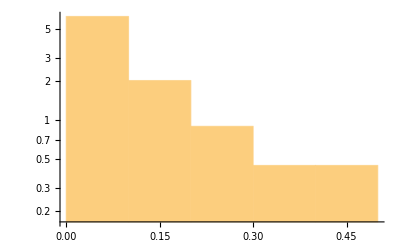

```mathematica
Histogram[getGoodEigs[Sort[Map[-Re[#]&,gaugebosons]]],Automatic,{"Log","PDF"}]
```

```mathematica
(* I don't believe this subalgebra stuff is currently correct...  Please ignore.*)
```

```mathematica
SubalgebraQ[fabc_,indices_, gens_] := Module[{comp=Complement[Range[1,Length[gens]],indices]},
AllTrue[Flatten[Table[fabc[[a]][[b]][[c]],{a,indices},{b,indices}, {c, comp}],2], PossibleZeroQ] &&
AllTrue[Table[AnyTrue[Map[Function[x,fabc[[x[[1]]]] [[x[[2]]]] [[c]]],Subsets[indices,{2}]
(*AllTrue[Table[fabc[[x[[1]]]] [[x[[2]]]] [[c]],{c, comp}],PossibleZeroQ]*)
], Not[PossibleZeroQ[#]]& ],{c,indices}],TrueQ]]
```

```mathematica
Subalgebras[fabc_, gens_] := Module[{allindices=Reverse[Subsets[Range[1,Length[gens]],{3,Length[gens]}]]},
DeleteDuplicates[Table[If[SubalgebraQ[fabc,indices,gens] == True, indices, {}], {indices, allindices}]]]
```

```mathematica
(*"Good" eigenvalues are considered to be positive and non-degenerate. Eigenvalues that are near zero (within machine precision) will typically be ~10^-18 to ~10^-20, so machinetol should be set large enough to exclude these values, but small enough to include legitimately small but non-zero eigenvalues.  If arbitrary precision is used to do all calculations, tol can be set much smaller which eliminates the problem (at ~10X performance penalty).*)
```

```mathematica
machinetol=10^-15;
```

```mathematica
tol=N[10^-50,100];
```

```mathematica
getGoodEigs[eigs_] := Reverse[TakeWhile[Reverse[eigs],#> machinetol&]]
```

```mathematica
showEigs[r_,n_,m_, dists_, pdfs_, inits_]:=Module[{eigs,eigdata,allparams, dists2, pdfs2},
eigs = getGoodEigs[getEigs[r,n,m]];
eigdata = Transpose[{Range[0,Length[eigs]-1], eigs}];
allparams= FindDistributionParameters[eigs,#,inits, ParameterEstimator->{"MaximumLikelihood",Method->"FindMaximum"}] & /@dists;
dists2 = MapThread[#1/.#2&,{dists, allparams}];
pdfs2 = MapThread[#1/.#2&,{pdfs, allparams}];
(*Print[eigs];*)
Print[DistributionFitTest[eigs,#]& /@dists2];
Show[{Histogram[eigs,Automatic,{"Log","PDF"}],(*Automatic->{n/10*Abs[Median[getDiffs[eigs]]]}*)
LogPlot[pdfs2, {xvar,0,Max[eigs]}, PlotLegends -> dists2]}, PlotRange -> Automatic]]
```

```mathematica
(*The following distributions are just shown for reference.  Simplified versions of this output are what appears in the draft.*)
```

```mathematica
wigner2dist= TransformedDistribution[u^2,u\[Distributed]WignerSemicircleDistribution[rad]];
```

```mathematica
wignerpdf=PDF[WignerSemicircleDistribution[rad],xvar]
```

Piecewise[{{(2 √(1-xvar^2/rad^2))/(π rad), -rad<xvar<rad}, {0, True}}]

```mathematica
wignercdf=CDF[WignerSemicircleDistribution[rad],xvar]
```

Piecewise[{{1/2+(xvar √(1-xvar^2/rad^2))/(π rad)+ArcSin[xvar/rad]/π, -rad<xvar<rad}, {1, xvar≥rad}, {0, True}}]

```mathematica
wigner2pdf=FullSimplify[PDF[wigner2dist,xvar]]
```

Piecewise[{{(2 (rad^2/(2 √(-1+rad^2/xvar) xvar)+(rad^2-2 xvar)/(2 √((rad^2-xvar) xvar))))/(π rad^2), rad>0&&(rad^2==xvar||(xvar>0&&rad^2≥xvar))}, {0, True}}]

```mathematica
wigner2cdf=CDF[wigner2dist,xvar]
```

Piecewise[{{1, rad>0&&rad^2-xvar<0}, {(2 (√((rad^2-xvar) xvar)+rad^2 ArcTan[1/(√(-1+rad^2/xvar))]))/(π rad^2), (rad^2-xvar==0&&rad>0)||(rad^2-xvar≥0&&rad>0&&xvar>0)}, {0, True}}]

```mathematica
(*NOTE: IMPORTANT The rewrite rules (See "UpValues") for WignerDistributionSquared (see below) are not yet quite firing in the correct order, so although this works with wigner2dist, it is ~15,000 times slower, so it may require running overnight.*)
```

FindDistributionParameters::nvsprt: The support of the distribution TransformedDistribution[x^2, x \[Distributed] WignerSemicircleDistribution[rad]] could not be determined. The validity of the data for TransformedDistribution[x^2, x \[Distributed] WignerSemicircleDistribution[rad]] could not be determined.

{Indeterminate}

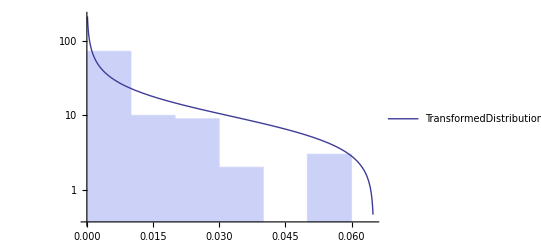
{20713.14186,-Graphics-}

```mathematica
showEigs[100,100,0,{wigner2dist},{wigner2pdf},{{rad,0.25}}] //Timing
```

```mathematica
(*However, a workaround for this is to simply copy and paste (which is bad, but oh well) the definition of showEigs to the top level, which works **perfectly**.*)
```

```mathematica
(*The following plots are using the full set of SUN generators in the 'defining' basis for Sqrt[y=m^2].*)
```

FindDistributionParameters::nvsprt: The support of the distribution TransformedDistribution[√x^2, x \[Distributed] WignerSemicircleDistribution[rad]] could not be determined. The validity of the data for TransformedDistribution[√x^2, x \[Distributed] WignerSemicircleDistribution[rad]] could not be determined.

FindMaximum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {8.24339×10^-14, 0.0000152588, 8.32666×10^-14}, is returned.

{1.}

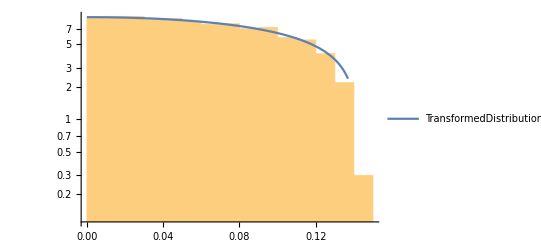

```mathematica
Module[{eigs,eigdata,allparams, dists2, pdfs2, dists={TransformedDistribution[Sqrt[u^2],u\[Distributed]WignerSemicircleDistribution[rad]]},
pdfs={PDF[TransformedDistribution[Sqrt[u^2],u\[Distributed]WignerSemicircleDistribution[rad]],xvar]},
inits={{{rad,Sqrt[2/100]}}}},
eigs = getGoodEigs[Sort[Flatten[Table[Map[Sqrt,getEigs[100^2-1,100,0]],{10}]]]];
eigdata = Transpose[{Range[0,Length[eigs]-1], eigs}];
allparams= MapThread[FindDistributionParameters[eigs,#1,#2, ParameterEstimator->{"MaximumLikelihood",Method->"FindMaximum"}] & ,{dists, inits}];
dists2 = MapThread[#1/.#2&,{dists, allparams}];
pdfs2 = MapThread[#1/.#2&,{pdfs, allparams}];
(*Print[eigs];*)
Print[DistributionFitTest[eigs,#]& /@dists2];
Show[{Histogram[eigs,Automatic,{"Log","PDF"}],
LogPlot[pdfs2, {xvar,0,Max[eigs]}, PlotLegends -> dists2]}, PlotRange ->Automatic]]
```

```mathematica
(*The purpose of this function is to show that for small r, the number of eigenvalues is 1. NOT equal to n, 2. depends on which generators get randomly chosen, and 3. depends on the basis.*)
showNumberOfEigs[r_,n_,m_, num_]:=Module[{numeigs= Table[Length[getGoodEigs[getEigs[r,n,m]]],{num}]},
Show[{Histogram[numeigs,Automatic,{"Log","PDF"}]}, PlotRange -> Automatic]]
```

```mathematica
(*Start of WignerDistributionSquared. Modified from the tutorial at http://www.wolfram.com/events/technology-conference/2011/presentations/CreateYourOwnDistributionWorkshop.zip*)
```

```mathematica
(*The output of TransformedDistribution is treated by mathematica as a symbolic expression (unless it happens to be of the form of a built-in distribution).  If you try to pass it to FindDistributionParameters or EstimatedDistribution, mathematica will happily symbolically recompute the CDF/PDF for *every single data point*!!  This is horrendously slow, so we can do it ourselves once and for all and use TagSet to point mathematica to our results.  All of the functions below can be rederived by plugging TransformedDistribution[u^2,u\[Distributed]WignerSemicircleDistribution[r]] into PDF, CDF, etc*)
```

```mathematica
(*The commented out lines are a relic from when there was ambiguity over whether the independent variable in WignerDistributionSquared was m^2 or Sqrt[m^2]*)
```

```mathematica
ClearAll[WignerDistributionSquared];
```

```mathematica
(*WignerDistributionSquared /:WignerDistributionSquared[r_] := ProbabilityDistribution[Piecewise[{{0, r > 0 && r^2 - x < 0}, {(2*(r^4/(2*(1 + 1/(-1 + r^2/x))*(-1 + r^2/x)^(3/2)*x^2) + (r^2 - 2*x)/(2*Sqrt[(r^2 - x)*x])))/(Pi*r^2), 
    (r^2 - x == 0 && r > 0) || (r^2 - x >= 0 && r > 0 && x > 0)}}, 0],{x,0,Infinity}]*)
```

```mathematica
(*Predicates*)
```

```mathematica
WignerDistributionSquared /: DistributionParameterAssumptions[WignerDistributionSquared[r_]]:= r∈Reals∧r>0
```

```mathematica
WignerDistributionSquared /: DistributionParameterQ[di:WignerDistributionSquared[r_]]:= Or[!NumericQ[r],(Positive[r]===True),Message[WignerDistributionSquared::posprm,r,1,di]]
```

```mathematica
WignerDistributionSquared/:Statistics`Library`DistributionNParameterQ[di:WignerDistributionSquared[r_]]:=Or[(Positive[r]===True),Message[WignerDistributionSquared::posprm,r,1,di]]
```

```mathematica
(*Distribution functions*)
```

```mathematica
WignerDistributionSquared /: DistributionDomain[WignerDistributionSquared[r_]?DistributionParameterQ]:= Interval[{0,Infinity}]
```

```mathematica
WignerDistributionSquared /: PDF[WignerDistributionSquared[r_]?DistributionParameterQ,y_]:= Function[x,Piecewise[{{0, r > 0 && r^2 - x < 0}, {(2*(r^4/(2*(1 + 1/(-1 + r^2/x))*(-1 + r^2/x)^(3/2)*x^2) + (r^2 - 2*x)/(2*Sqrt[(r^2 - x)*x])))/(Pi*r^2), 
    (r^2 - x == 0 && r > 0) || (r^2 - x >= 0 && r > 0 && x > 0)}}, 0],Listable][y]
```

```mathematica
(*WignerDistributionSquared /: PDF[WignerDistributionSquared[r_]?DistributionParameterQ,y_]:= Function[x,Piecewise[{{0, r > 0 && r^2 - x^2 < 0}, {(2*(r^4/(2*(1 + 1/(-1 + r^2/x^2))*(-1 + r^2/x^2)^(3/2)*x^2) + (r^2 - 2*x^2)/(2*Sqrt[(r^2 - x^2)*x^2])))/(Pi*r^2), 
    (r^2 - x^2 == 0 && r > 0) || (r^2 - x^2 >= 0 && r > 0 && x > 0)}}, 0],Listable][y]*)
```

```mathematica
WignerDistributionSquared /: CDF[WignerDistributionSquared[r_]?DistributionParameterQ,y_]:= Function[x,Piecewise[{{1, r > 0 && r^2 - x < 0}, {(2*(Sqrt[(r^2 - x)*x] + r^2*ArcTan[1/Sqrt[-1 + r^2/x]]))/(Pi*r^2), 
    (r^2 - x == 0 && r > 0) || (r^2 - x >= 0 && r > 0 && x > 0)}}, 0],Listable][y]
```

```mathematica
(*WignerDistributionSquared /: CDF[WignerDistributionSquared[r_]?DistributionParameterQ,y_]:= Function[x,Piecewise[{{1, r > 0 && r^2 - x^2 < 0}, {(2*(Sqrt[(r^2 - x^2)*x^2] + r^2*ArcTan[1/Sqrt[-1 + r^2/x^2]]))/(Pi*r^2), 
    (r^2 - x^2 == 0 && r > 0) || (r^2 - x^2 >= 0 && r > 0 && x > 0)}}, 0],Listable][y]*)
```

```mathematica
WignerDistributionSquared /: SurvivalFunction[WignerDistributionSquared[r_]?DistributionParameterQ,y_]:= Function[x,Piecewise[{{1, r <= 0 || (r^2 - x > 0 && x <= 0)}, {1 - (2*(Sqrt[(r^2 - x)*x] + r^2*ArcTan[1/Sqrt[-1 + r^2/x]]))/(Pi*r^2), (r^2 - x == 0 && r > 0) || (r^2 - x >= 0 && r > 0 && x > 0)}}, 0],Listable][y]
```

```mathematica
(*WignerDistributionSquared /: SurvivalFunction[WignerDistributionSquared[r_]?DistributionParameterQ,y_]:= Function[x,Piecewise[{{1, r <= 0 || (r^2 - x^2 > 0 && x <= 0)}, {1 - (2*(Sqrt[(r^2 - x^2)*x^2] + r^2*ArcTan[1/Sqrt[-1 + r^2/x^2]]))/(Pi*r^2), (r^2 - x^2 == 0 && r > 0) || (r^2 - x^2 >= 0 && r > 0 && x > 0)}}, 0],Listable][y]*)
```

```mathematica
WignerDistributionSquared /: HazardFunction[WignerDistributionSquared[r_]?DistributionParameterQ,y_]:= Function[x,Piecewise[{{0, (r^2 - x > 0 && x <= 0) || r^2 - x < 0}}, (2*(r^2/(2*Sqrt[-1 + r^2/x]*x) + (r^2 - 2*x)/(2*Sqrt[(r^2 - x)*x])))/
   (Pi*r^2*(1 - (2*(Sqrt[(r^2 - x)*x] + r^2*ArcTan[1/Sqrt[-1 + r^2/x]]))/(Pi*r^2)))],Listable][y]
```

```mathematica
(*WignerDistributionSquared /: HazardFunction[WignerDistributionSquared[r_]?DistributionParameterQ,y_]:= Function[x,Piecewise[{{0, (r^2 - x^2 > 0 && x <= 0) || r^2 - x^2 < 0}}, (2*(r^2/(2*Sqrt[-1 + r^2/x^2]*x^2) + (r^2 - 2*x^2)/(2*Sqrt[(r^2 - x^2)*x^2])))/
   (Pi*r^2*(1 - (2*(Sqrt[(r^2 - x^2)*x^2] + r^2*ArcTan[1/Sqrt[-1 + r^2/x^2]]))/(Pi*r^2)))],Listable][y]*)
```

```mathematica
(*General Moments*)
```

```mathematica
WignerDistributionSquared/:Moment[WignerDistributionSquared[r_]?DistributionParameterQ,k_]:=Function[n,Piecewise[{{(r^(2*n)*Gamma[1/2 + n])/(Sqrt[Pi]*Gamma[2 + n]), r > 0}}, 0],Listable][k]
```

```mathematica
WignerDistributionSquared/:CentralMoment[di:WignerDistributionSquared[r_]?DistributionParameterQ,k_Integer?NonNegative]:=Statistics`Library`UnivariateMomentsConvert[di,k,Moment->CentralMoment]
```

```mathematica
WignerDistributionSquared/:FactorialMoment[di:WignerDistributionSquared[r_]?DistributionParameterQ,k_Integer?NonNegative]:=Statistics`Library`UnivariateMomentsConvert[di,k,Moment->FactorialMoment]
```

```mathematica
WignerDistributionSquared/:Cumulant[di:WignerDistributionSquared[r_]?DistributionParameterQ,k_Integer?NonNegative]:=Statistics`Library`UnivariateMomentsConvert[di,k,Moment->Cumulant]
```

```mathematica
(*Named Moments*)
```

```mathematica
WignerDistributionSquared/:Mean[WignerDistributionSquared[r_]?DistributionParameterQ]:=r^2/4
```

```mathematica
WignerDistributionSquared/:Variance[WignerDistributionSquared[r_]?DistributionParameterQ]:=r^4/16
```

```mathematica
WignerDistributionSquared/:StandardDeviation[WignerDistributionSquared[r_]?DistributionParameterQ]:=r^2/4
```

```mathematica
WignerDistributionSquared/:Skewness[WignerDistributionSquared[r_]?DistributionParameterQ]:=1
```

```mathematica
WignerDistributionSquared/:Kurtosis[WignerDistributionSquared[r_]?DistributionParameterQ]:=3
```

```mathematica
(*Generating Function*)
```

```mathematica
WignerDistributionSquared/:GeneratingFunction[WignerDistributionSquared[r_]?DistributionParameterQ,t_]:=E^((1/2)*I*r^2*t)*(BesselJ[0, (r^2*t)/2] - I*BesselJ[1, (r^2*t)/2])
```

```mathematica
(*Quantile, Median, InverseCDF, InverseSurvivalFunction not implemented*)
```

```mathematica
(*Random Number Generation not implemented*)
```

```mathematica
(*Parameter Estimation*)
```

```mathematica
WignerDistributionSquared/:Statistics`Library`AcceptableDistributedDataQ[WignerDistributionSquared[r_],data_]:=VectorQ[data,NumericQ]&&(Positive[Min[data]]===True)
```

```mathematica
WignerDistributionSquared/:Statistics`Library`DefaultEstimator[WignerDistributionSquared[r_],"MaximumLikelihood"]:="FindRoot" (* or "FindMaximum", "NMinimize", "Solve", etc.*)
```

```mathematica
WignerDistributionSquared/:Statistics`Library`DistributionParameterEstimation[data_,Unevaluated[WignerDistributionSquared[r_]],start_,optlist_,"MaximumLikelihood",caller_]:=
Module[{rr,f,j,r0,fopts,res,mean},
f[rr_Real]=Mean[Piecewise[{{-Infinity, (rr^2 - data > 0 && data <= 0) || rr^2 - data< 0 || rr <= 0}}, Log[(2*(rr^2/(2*Sqrt[-1 + rr^2/data]*data) + (rr^2 - 2*data)/(2*Sqrt[(rr^2 - data)*data])))/(Pi*rr^2)]]];
j[rr_Real]=Mean[Piecewise[{{-((rr^2 - 2*data)/(rr^3 - rr*data)), rr^2 >= data}}, 0]];
fopts=FilterRules[optlist,Options@FindRoot];
mean=Mean[Select[Clip[data,{0,r^2},{0,0}],Positive]];
r0=r/.FindRoot[r^2/4==mean,{r,1},Evaluate[fopts]];
If[NumberQ[r0],res=FindRoot[f[r]==0,{r,r0},Jacobian->{{j[r]}},Evaluate[fopts]];
If[ListQ[res],res,res=$Failed],res=$Failed];
Clear[f,j];
res]
```

```mathematica
(*WignerDistributionSquared/:Statistics`Library`DistributionParameterEstimation[data_,Unevaluated[WignerDistributionSquared[r_]],start_,optlist_,"MaximumLikelihood",caller_]:=
Module[{rr,f,j,r0,fopts,res,mean},
f[rr_Real]=Mean[Piecewise[{{-Infinity, (rr^2 - data^2 > 0 && data^2 <= 0) || rr^2 - data^2< 0 || rr <= 0}}, Log[(2*(rr^2/(2*Sqrt[-1 + rr^2/data^2]*data^2) + (rr^2 - 2*data^2)/(2*Sqrt[(rr^2 - data^2)*data^2])))/(Pi*rr^2)]]];
j[rr_Real]=Mean[Piecewise[{{-((rr^2 - 2*data^2)/(rr^3 - rr*data^2)), rr^2 >= data^2}}, 0]];
fopts=FilterRules[optlist,Options@FindRoot];
mean=Mean[Select[Clip[data,{0,r^2},{0,0}],Positive]];
r0=r/.FindRoot[r^2/4==mean,{r,1},Evaluate[fopts]];
If[NumberQ[r0],res=FindRoot[f[r]==0,{r,r0},Jacobian->{{j[r]}},Evaluate[fopts]];
If[ListQ[res],res,res=$Failed],res=$Failed];
Clear[f,j];
res]*)
```

```mathematica
(*End of WignerDistributionSquared*)
```

```mathematica
(*I don't remember why these next two functions were here. Please ignore.*)
```

```mathematica
(*This transformed probability distribution corresponds to the positive root of a quadratic formula.*)
quadeigplusdist=TransformedDistribution[(a^2+d^2+Sqrt[(a^2+d^2)^2+4b^2*c^2])/2,{a\[Distributed]NormalDistribution[0,1], b\[Distributed]NormalDistribution[0,1], c\[Distributed]NormalDistribution[0,1], d\[Distributed]NormalDistribution[0,1]}];
```

```mathematica
(*This transformed probability distribution corresponds to the positive root of a quadratic formula.*)
quadeigminusdist=TransformedDistribution[(a^2+d^2-Sqrt[(a^2+d^2)^2+4b^2*c^2])/2,{a\[Distributed]NormalDistribution[0,1], b\[Distributed]NormalDistribution[0,1], c\[Distributed]NormalDistribution[0,1], d\[Distributed]NormalDistribution[0,1]}];
```

```mathematica
(*The following functions are used for fitting the eigenvalues to a particular functional form.  They are used to find numerical values for the scaling laws.  Note that since we are no longer interested in the scaling laws, this code can be ignored.*)
```

```mathematica
getLinearFit[goodEigs_]:=
Module[{goodData=Transpose[{Range[1,Length[goodEigs]], goodEigs}],m,x,b},
(*Use Rest here so the fitting algorithm doesn't calculate 0^b and thus create a singular jacobian*)
Map[Last,FindFit[goodData,m*x+b,{m,b},x]]]
```

```mathematica
getExpFit[goodEigs_,offset_:0, m0_:0]:=
Module[{goodData=Transpose[{Range[1,Length[goodEigs]], goodEigs, goodEigs}],a,j,x,b},
(*This is the scaling relation from the original DDM I paper: Arxiv 1208.0336 equation 3.5*)
Map[Last,FindFit[goodData,m0+a*(j+offset)^b,{{a,10^-10},{b,2.0}},{j,x}, MaxIterations-> 100]]](*Min[goodEigs]*)
```

```mathematica
getScalingModel1[goodEigs_,offset_:0, m0_:0]:=
Module[{goodData=Transpose[{Range[1,Length[goodEigs]], goodEigs}],a,b, m, j},
(*This is the scaling relation from the original DDM I paper: Arxiv 1208.0336 equation 3.5*)
NonlinearModelFit[goodData,{m0+a*(j+offset)^b},{{a,10^-10},{b,2.0}},{j}]](*Min[goodEigs]*)
```

```mathematica
getScalingModel2[goodEigs_,offset_:0, m0_:0]:=
Module[{goodData=Transpose[{Range[1,Length[goodEigs]], goodEigs}],a,b, m, j},
(*This is the scaling relation from the original DDM I paper: Arxiv 1208.0336 equation 3.5*)
NonlinearModelFit[goodData,{m+a*(j+offset)^b},{{m,m0},{a,10^-10},{b,2.0}},{j}]](*Min[goodEigs]*)
```

```mathematica
getModelParameters[fittedmodel_] := Map[Last,fittedmodel["BestFitParameters"]]
```

```mathematica
getPiecewiseExpFit[numpieces_,goodEigs_] := Transpose[Map[getExpFit[First[#],Last[#]*Length[goodEigs]/numpieces, First[goodEigs]]&,
Transpose[{Partition[goodEigs,Length[goodEigs]/numpieces],Range[0,numpieces-1]}]]]
```

```mathematica
(*Since the fitting procedure is numerically sensitive, this function performs an average fit on (num) realizations of the data.  The rank of the eigenvalue (i.e. the i-th eigenvalue) is on the x-axis, and the value of the eigenvalue is on the y-axis.*)
showAverageFits[r_,n_,m_,num_,fit_, fn_: Identity] :=
Module[{goodEigs,avgExpFits,avgExpFit, allData},
goodEigs=Table[Map[fn,getGoodEigs[getEigs[r,n,m]]],{num}];(*getEigs[r,n,m] expeigs*)
avgExpFits=Map[getExpFit[Take[#,Floor[fit*Length[#]]],0,First[#]]&,goodEigs];
avgExpFit=Map[Mean,Transpose[avgExpFits]];
allData=Flatten[Map[Transpose[{Range[0,Length[#]-1], #}]&,goodEigs],1];
Print["Avg exp fit: " + avgExpFit];
Show[ListLogPlot[allData],
LogPlot[Mean[Map[Min,goodEigs]]+First[avgExpFit]*j^Last[avgExpFit], {j,0,Length[First[goodEigs]]}]]]
```

```mathematica
(*This function is used to determine the pdf of the spacing between the eigenvalues.*)
showDiffs[r_,n_,m_]:=Module[{eigs,diffs,dists, pdfs,u,lambda1,lambda2,x},
eigs=getGoodEigs[getEigs[r,n,m]];
diffs = getDiffs[eigs];
dists = EstimatedDistribution[diffs,#] & /@ {ExponentialDistribution[lambda1] (*,TransformedDistribution[u^2,u\[Distributed]ExponentialDistribution[lambda2]]*)};
pdfs=D[CDF[#,x],x]&/@dists;
(*Print[diffs];*)
Print[DistributionFitTest[diffs,#]& /@dists];
Show[{Histogram[diffs,Automatic, {"Log","PDF"}],(*Automatic->{n/10*Abs[Median[getDiffs[diffs]]]}*)
LogPlot[pdfs, {x,0,Max[diffs]}, PlotLegends->dists]},PlotRange -> {0,Automatic}]]
```

{0.000294685}

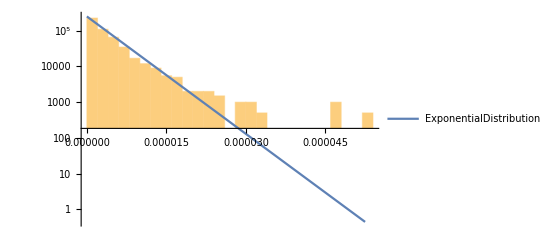

```mathematica
showDiffs[1,1000,0]
```

```mathematica
(*Returns the averages between successive pairs in a list of numbers*)
getAvgs[nums_]:= Map[Mean,Partition[nums,2,1]]
```

```mathematica
a=N[2*Sqrt[1/1000]]
```

0.0632456

```mathematica
a=2*Sqrt[r/n]
```

2 √(r/n)

```mathematica
(*The following functions were used to assist in the derivation of various analytic results.  In particular, the cdf is used below to calculate the expectation value of eigenvalues.  See further comments below.*)
```

```mathematica
wigner2pdf=PDF[wigner2dist,xvar]/. rad ->a
```

Piecewise[{{(2 (a^2/(2 √(-1+a^2/xvar) xvar)+(a^2-2 xvar)/(2 √((a^2-xvar) xvar))))/(a^2 π), (a^2-xvar==0&&a>0)||(a^2-xvar≥0&&a>0&&xvar>0)}, {0, True}}]

```mathematica
wigner2cdf=CDF[wigner2dist,xvar]/. rad ->a
```

Piecewise[{{1, 0.004-xvar<0}, {159.155 (√((0.004-xvar) xvar)+0.004 ArcTan[1/(√(-1+0.004/xvar))]), 0.004-xvar==0||(0.004-xvar≥0&&xvar>0)}, {0, True}}]

```mathematica
(*2 term taylor expansions of wigner2cdf around 0 & rad^2*)
```

```mathematica
wigner2cdfs20=Normal[Series[wigner2cdf,{xvar,0,2}, Assumptions-> {xvar ∈ Reals,rad ∈ Reals, xvar < rad, xvar > 0, rad > 0}]]
```

20.1317 √xvar-838.82 xvar^(3/2)

```mathematica
(*For some reason, expanding around xvar/rad=1 gives the negative of the CDF. ???*)
```

```mathematica
wigner2cdfs21=Normal[Series[wigner2cdf,{xvar,rad^2-d,2}, Assumptions-> {xvar ∈ Reals,rad ∈ Reals, xvar < rad, xvar > 0, rad > 0}]]
```

Piecewise[{{1, (d==0&&rad^2-xvar<0)||d<0}, {(2 √d √(-d+rad^2))/(π rad^2)+((√(-d/(d-rad^2)))/(d π)-1/(√d π √(-d+rad^2))+(2 √d)/(π rad^2 √(-d+rad^2))) (d-rad^2+xvar)+((√d rad^2+2 d √(-d/(d-rad^2)) √(-d+rad^2)-rad^2 √(-d/(d-rad^2)) √(-d+rad^2)) (d-rad^2+xvar)^2)/(4 d^2 π (d-rad^2) √(-d+rad^2))-(2 ArcTan[(√(-d/(d-rad^2)) (d-rad^2))/d])/π, True}}]

```mathematica
Simplify[wigner2cdfs21/.xvar -> rad^2]
```

Piecewise[{{1, d<0}, {(-4 d^(3/2)+3 √d rad^2-6 d √(-d/(d-rad^2)) √(-d+rad^2)+5 rad^2 √(d/(-d+rad^2)) √(-d+rad^2)+8 (-d+rad^2)^(3/2) ArcTan[1/(√(-d/(d-rad^2)))])/(4 π (-d+rad^2)^(3/2)), True}}]

```mathematica
Limit[%,d-> 0]
```

√(1/rad^2) √(rad^2)

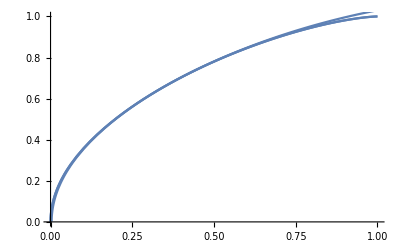

```mathematica
Show[Plot[wigner2cdf^.5/.{rad-> 1},{xvar,0,1}],
Plot[wigner2cdfs20^.5/.{rad-> 1},{xvar,0,1}],
Plot[(-wigner2cdfs21)^.5/.{rad-> 1},{xvar,0,1}]
]
```

```mathematica
(*Range over n-1 and manually append a^2 to the results list because NSolve chokes on the endpoint.*)
getCDFMaxes[n_]  := Join[Map[Last[First[First[NSolve[wigner2cdf-#/n==0 && xvar≥0 && xvar≤a^2,{xvar}]]]] &, Range[0,n-1]], {a^2}]
```

```mathematica
cdfmaxes=getCDFMaxes[1000];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve :: ratnz will be suppressed during this calculation.

```mathematica
mincdfmax=Solve[Normal[Series[wigner2cdf,{xvar,0,1}]]-1/n==0 && xvar≥0 && xvar≤a^2,{xvar}]
```

{{xvar→ConditionalExpression[(π^2 r)/(4 n^3),n>π/4&&r>0]}}

```mathematica
(*Approximate analytic expression for the smallest eigenvalue y_0*)
```

```mathematica
mineigexp=Simplify[Integrate[wigner2pdf*xvar,{xvar,0,(π^2 r)/(4 n^3)}, Assumptions->  n ∈ Integers&& r∈ Integers&& n>0&&r>0]]
```

(r (π √(16 n^2-π^2) (-8 n^2+π^2)+128 n^4 ArcTan[π/(√(16 n^2-π^2))]))/(64 n^5 π)

```mathematica
(*Mathematica's expectation value function (Exp) is very slow, so we reimplement it here.  We also need to multiply by n=1000.
Take the real part because the NIntegrate may calculate a very small imaginary part for the last fake eigenvalue.*)
GetExpectationValue[{xmin_,xmax_}] := Re[NIntegrate[wigner2pdf*xvar*1000,{xvar,xmin,xmax}]]
```

```mathematica
(*Generate 'fake' eigenvalues based on the expectation of wigner2pdf in bins.  We were using 'fake' eigenvalues because the fitting procedure for the scaling laws is numerically sensitive, and 'fake' eigenvalues are deterministic.  Note that since we are no longer interested in the scaling laws, this code can be ignored.*)
getExpEigs[maxcdfs_] := Map[GetExpectationValue,Partition[maxcdfs,2,1]]
```

```mathematica
expeigs=getExpEigs[cdfmaxes];
```

```mathematica
(*Show scaling for eigenvalues*)
```

```mathematica
{avgexpdm,avgexpdelta}=getExpFit[expeigs]
```

{7.97399×10^-11,2.54669}

```mathematica
{dms,deltas}=getPiecewiseExpFit[25,getEigs[1,1000,0]](*getEigs[1,1000,0]*)
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit :: cvmit will be suppressed during this calculation.

{{1.46497×10^-9,3.26446×10^-9,1.80162×10^-9,3.16788×10^-9,1.89656×10^-9,2.23106×10^-9,1.51811×10^-9,1.43583×10^-9,2.49592×10^-9,1.64803×10^-9,1.50166×10^-9,1.32575×10^-9,9.77546×10^-10,9.86423×10^-10,3.96737×10^-10,9.65946×10^-10,4.07294×10^-10,4.86413×10^-10,2.68127×10^-10,1.07401×10^-10,5.52327×10^-11,4.72745×10^-11,1.00632×10^-11,1.29831×10^-11,8.98353×10^-13},{2.14507,1.93277,2.06231,1.94633,2.04828,2.01826,2.08909,2.09726,2.00163,2.07225,2.08757,2.10805,2.15736,2.1553,2.29924,2.15988,2.29378,2.26679,2.35769,2.49535,2.59485,2.61825,2.84672,2.81211,3.20692}}

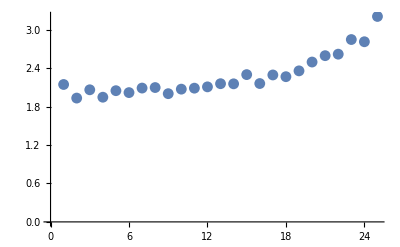

```mathematica
ListPlot[Transpose[{Range[1,25],deltas}],PlotRange->{{0,25},{0,Max[deltas]}}]
```

```mathematica
(*Show scaling for eigenvalue spacings*)
```

```mathematica
expdiffs = Map[Last[#]-First[#]&,Partition[getEigs[1,1000,0],2,1]];
```

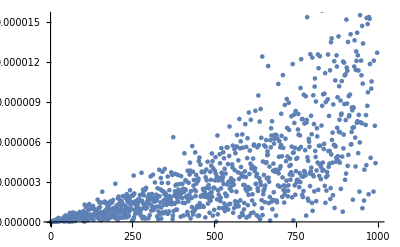

```mathematica
ListPlot[expdiffs]
```

```mathematica
{sdms,sdeltas}=getPiecewiseExpFit[25,Join[{0},expdiffs]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit :: cvmit will be suppressed during this calculation.

{{6.93344×10^-9,2.28429×10^-9,6.65891×10^-10,4.60188×10^-10,9.62427×10^-10,8.08292×10^-10,1.77379×10^-7,2.50557×10^-12,3.81242×10^-14,1.19868×10^-12,1.17007×10^-7,4.82084×10^-7,3.24498×10^-12,2.04539×10^-8,2.74984×10^-8,1.80675×10^-14,3.41371×10^-10,4.21786×10^-11,7.27781×10^-11,3.57585×10^-8,2.1061×10^-12,1.37218×10^-14,4.35778×10^-15,4.73049×10^-15,1.38455×10^-17},{0.864349,1.19628,1.42598,1.4822,1.31641,1.33171,0.35787,2.34322,3.02743,2.4097,0.491442,0.263644,2.1972,0.800449,0.752499,2.98024,1.44561,1.76538,1.68572,0.755265,2.22703,2.96925,3.15215,3.13792,4.07869}}

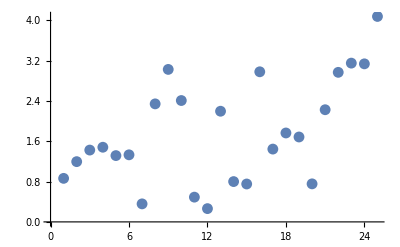

```mathematica
ListPlot[Transpose[{Range[1,25],sdeltas}],PlotRange->{{0,25},{0,Max[sdeltas]}}]
```

```mathematica
(*Fit data for Tables 1-4 over explicit matrix sizes*)
```

```mathematica
matrixDims={3,4,5,6,7,8,9,10,15,20,25,50,100,200,1000};
```

```mathematica
matrixEigs= Map[getGoodEigs[getEigs[1,#,0]]&,matrixDims];
```

```mathematica
models1 = Map[getScalingModel1[#]&,matrixEigs];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
tabledata1 = Map[Join[{Last[First[#["Data"]]]},getModelParameters[#],{#["RSquared"]}]&,models1];
```

```mathematica
tabledata1 // MatrixForm
```

(0.0318228 | 5.59574×10^-8 | 15.0862 | 0.990256
0.00935544 | 0.0277158 | 2.17975 | 0.990003
0.00254691 | 0.00411182 | 3.05954 | 0.998937
0.00104517 | 0.000942931 | 3.53368 | 0.999274
0.000957937 | 0.00365906 | 2.39403 | 0.997405
0.0004962 | 0.00160899 | 2.59399 | 0.972872
0.000751676 | 0.00400298 | 1.94252 | 0.990552
0.000721476 | 0.000324902 | 2.99338 | 0.989353
0.00203125 | 0.0000280688 | 3.3451 | 0.989135
6.84286×10^-6 | 0.0000326456 | 2.86481 | 0.997887
7.69984×10^-7 | 0.0000171865 | 2.79717 | 0.995903
2.35766×10^-6 | 3.05736×10^-6 | 2.55842 | 0.998735
5.91335×10^-7 | 2.06312×10^-7 | 2.61394 | 0.996308
1.94406×10^-7 | 2.14468×10^-8 | 2.56804 | 0.997885
1.49486×10^-10 | 7.6724×10^-11 | 2.55245 | 0.997325)

```mathematica
models2 = Map[getScalingModel2[#]&,matrixEigs];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
tabledata2 = Map[Join[getModelParameters[#],{#["RSquared"]}]&,models2];
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
tabledata2 // MatrixForm
```

(0.0568014 | 5.78201×10^-8 | 14.9976 | 0.998419
-0.0585596 | 0.0537191 | 1.76782 | 0.993097
-0.00686259 | 0.00480273 | 2.96967 | 0.999074
0.00429929 | 0.000813334 | 3.6124 | 0.999363
-0.000049135 | 0.00366517 | 2.39322 | 0.997405
0.0171577 | 0.000606866 | 3.04902 | 0.974779
-0.0164577 | 0.00699472 | 1.70941 | 0.9923
0.0120864 | 0.000129482 | 3.3832 | 0.991232
0.00895713 | 8.48469×10^-6 | 3.77973 | 0.991805
0.00168801 | 0.000025271 | 2.94845 | 0.998037
0.00120747 | 0.0000135898 | 2.8686 | 0.996025
0.000889311 | 2.02608×10^-6 | 2.66195 | 0.998989
0.000682507 | 9.40438×10^-8 | 2.7828 | 0.996917
0.000311148 | 9.62073×10^-9 | 2.71797 | 0.99839
0.0000665863 | 2.49426×10^-11 | 2.71406 | 0.997902)

```mathematica
models3 = Map[getScalingModel1[TakePercent[#,80]]&,matrixEigs];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
tabledata3 = Map[Join[{Last[First[#["Data"]]]},getModelParameters[#],{#["RSquared"]}]&,models3];
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
tabledata3 // MatrixForm
```

(0.0318228 | 5.46888×10^-8 | 20.5457 | 0.873725
0.00935544 | 1.16023×10^-6 | 11.4836 | 0.946826
0.00254691 | 0.00216635 | 3.55696 | 0.999651
0.00104517 | 0.000830103 | 3.67458 | 0.995678
0.000957937 | 0.00591304 | 2.07348 | 0.990694
0.0004962 | 0.00516963 | 1.94415 | 0.990231
0.000751676 | 0.0022813 | 2.26478 | 0.982757
0.000721476 | 0.00253231 | 1.91914 | 0.993675
0.00203125 | 0.000110821 | 2.7825 | 0.982157
6.84286×10^-6 | 0.0000474371 | 2.72727 | 0.995909
7.69984×10^-7 | 0.0000258045 | 2.65048 | 0.990583
2.35766×10^-6 | 6.23226×10^-6 | 2.35487 | 0.99848
5.91335×10^-7 | 9.12036×10^-7 | 2.26043 | 0.999226
1.94406×10^-7 | 1.09015×10^-7 | 2.23485 | 0.999655
1.49486×10^-10 | 7.74739×10^-10 | 2.19634 | 0.999825)

```mathematica
models4 = Map[getScalingModel1[TakePercent[#,60]]&,matrixEigs];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
tabledata4 = Map[Join[{Last[First[#["Data"]]]},getModelParameters[#],{#["RSquared"]}]&,models4];
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
tabledata4 // MatrixForm
```

(0.0318228 | 0.0318228 | 2. | 1.
0.00935544 | 2.10362×10^-8 | 21.9662 | 0.988356
0.00254691 | 2.61896×10^-10 | 3.57909 | 2.50749×10^-7
0.00104517 | 2.63469×10^-10 | 3.56397 | 5.73765×10^-7
0.000957937 | 0.00316702 | 2.6001 | 0.990121
0.0004962 | 0.00210244 | 2.715 | 0.983983
0.000751676 | 0.000282018 | 3.60903 | 0.994525
0.000721476 | 0.00191788 | 2.08892 | 0.982192
0.00203125 | 0.000594919 | 1.99357 | 0.995459
6.84286×10^-6 | 0.000075892 | 2.52792 | 0.984025
7.69984×10^-7 | 0.00010446 | 2.08729 | 0.993599
2.35766×10^-6 | 0.0000160452 | 2.05736 | 0.998965
5.91335×10^-7 | 1.59227×10^-6 | 2.11785 | 0.999311
1.94406×10^-7 | 1.95181×10^-7 | 2.10767 | 0.999779
1.49486×10^-10 | 1.4566×10^-9 | 2.09429 | 0.999962)

```mathematica
deltas=Map[First[Rest[Rest[#]]]&,tabledata1]
```

{15.0862,2.17975,3.05954,3.53368,2.39403,2.59399,1.94252,2.99338,3.3451,2.86481,2.79717,2.55842,2.61394,2.56804,2.55245}

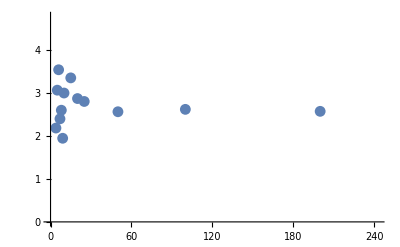

```mathematica
ListPlot[Transpose[{matrixDims,deltas}],PlotRange->Automatic](*{{0,Max[matrixDims]},{0,Max[deltas]}}*)
```

```mathematica
expDeltam=First[Rest[expeigs]]-First[expeigs]
```

4.93481×10^-9

```mathematica
(*Plot CDFs and scaling laws*)
```

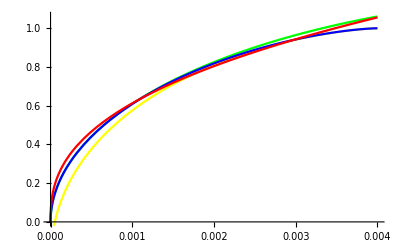

```mathematica
Show[{Plot[wigner2cdfs20,{xvar,0,a^2}, PlotStyle->{Green}],
Plot[1-16/(3*Sqrt[2]*Pi)*(1-x^(1/2)/a)^(3/2),{x,0,a^2}, PlotStyle-> {Yellow}],
Plot[wigner2cdf,{xvar,0,a^2}, PlotStyle->{Blue}],
Plot[((xvar-0)/avgexpdm)^(1/avgexpdelta)/1000,{xvar,0,a^2}, PlotStyle->{Red}]
}]
```

```mathematica
(*The average scaling law does not fit the entire spectrum of eigenvalues well simultaneously.*)
```

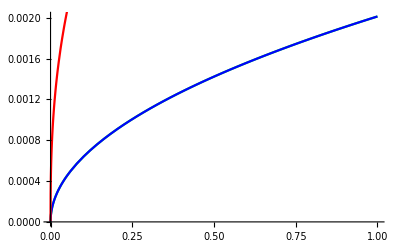

```mathematica
Show[{Plot[wigner2cdfs2,{xvar,0,10^-8}, PlotStyle->{Green}],
Plot[wigner2cdf,{xvar,0,10^-8}, PlotStyle->{Blue}],
Plot[(xvar/avgexpdm)^(1/avgexpdelta)/1000,{xvar,0,10^-8}, PlotStyle->{Red}]}]
```

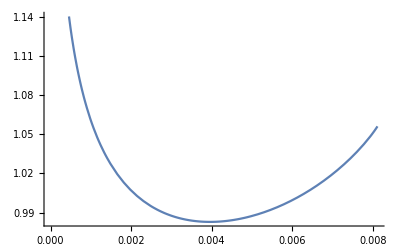

```mathematica
Plot[(((xvar-0)/dm)^(1/delta)/1000)/wigner2cdf,{xvar,First[expeigs],a^2}]
```

```mathematica
(*The average inverted scaling law differs from the exact cdf by no more than a factor of ~3.3*)
```

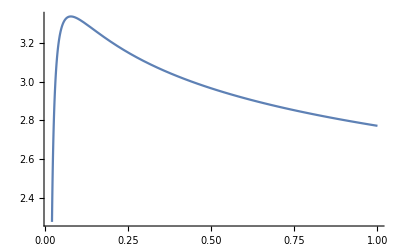

```mathematica
Plot[(((xvar-First[expeigs])/dm)^(1/delta)/1000)/wigner2cdf,{xvar,First[expeigs],10^-7}]
```

```mathematica
(*misc.*)
```

```mathematica
DropWhile [list_,crit_] := Reverse[TakeWhile[Reverse[list],crit]](*Need to negate criterion due to reverse*)
```

```mathematica
TakePercent[list_, percent_] := Module[{num= Floor[Length[list]*percent/100]}, Take[list, num]]
```

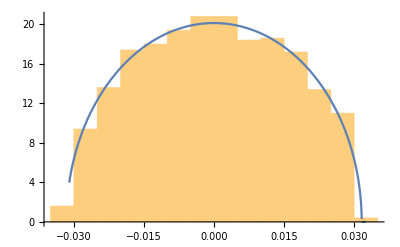

```mathematica
Module[{eigs=Map[Re,Eigenvalues[makeRandMatrixReal[0,1000]]](*RandomVariate[WignerSemicircleDistribution[1],10000]*)},
Show[{Histogram[eigs,Automatic,"PDF"],
Plot[PDF[WignerSemicircleDistribution[Sqrt[1/1000]],x], {x,Min[eigs],Max[eigs]}]}, PlotRange -> Automatic]]
```

```mathematica
(*Here are some functions pertaining to the interactions, injection spectra, etc.*)
```

```mathematica
(*This is the annihilation cross section, as determined from simplifying equation 3 in the designing ddm ensembles paper.*)
sigma[m_,mX_] := 1/(m^2*(1-mX^2/(4*m^2))^2)
```

```mathematica
(*This is an *approximation* of the abundance.  This function is a simplified version of Kolb & Turner eqns 5.44 & 5.45 (i.e. we have ignored all multiplicative prefactors and logarithmic corrections).  We are basically just computing 1 / \sigma where \sigma is the annihilation cross section.*)
Omega[m_, mX_] := 1/sigma[m,mX]
```

```mathematica
(*This is the decay rate (WITHOUT the random overlap), as determined by eq 6.2 of the draft*)
Decay[m_] := m^3
```

```mathematica
(*This function returns a list of {x,y} pairs where the x's are the eigenvalues of an explicitly generated random matrix and the y's are Gamma[x] * the random overlap in eq 6.2 of the draft. *)
computeDecay[r_,n_,M_] := Module[{mat=makeMatrix[r,n,M] // N,evals,evecs,decay,overlap,rvec=makeRandUnitVector[n]},
{evals,evecs}=Eigensystem[mat];
evals = Reverse[ Map[Sqrt[2*#]&,evals]]; evecs=Reverse[evecs];
overlap=Map[Re[#]^2&,Table[1/2*(evecs[[i]]+Map[Conjugate,evecs[[i]]]).rvec,{i,1,n}]];
decay=Table[{evals[[i]],Decay[evals[[i]]]*overlap[[i]]}, {i,1,Length[evals]}]
]
```

```mathematica
(*This function returns a list of {x,y} pairs where the x's are the eigenvalues of an explicitly generated random matrix and the y's are sigma[x]. *)
computeAnnihilation[r_,n_,M_, seed_:0] := Module[{mat=makeMatrix[r,n,M, seed] // N,evals,annihilation},
evals = Map[Sqrt[2*#]&,Reverse[Eigenvalues[mat]]];
annihilation=Table[{evals[[i]],sigma[evals[[i]]]}, {i,1,Length[evals]}]
]
```

```mathematica
(*This function returns a list of {x,y} pairs where the x's are the eigenvalues of an explicitly generated random matrix and the y's are omega[x]. *)
computeAbundance[r_,n_,M_, mX_, seed_:0] := Module[{mat=makeMatrix[r,n,M, seed] // N,evals,abundance},
evals = Map[Sqrt[2*#]&,Reverse[Eigenvalues[mat]]];
abundance=Table[{evals[[i]],Omega[evals[[i]]]}, {i,1,Length[evals]}]
]
```

```mathematica
(*Compute Abundance as a function of the Decay rate, not mass.  Why were we doing this again?*)
computeAbundanceDecay[r_,n_,M_] := Module[{mat=makeMatrix[r,n,M] // N,evals,evecs,overlap,rvec=makeRandUnitVector[n]},
{evals,evecs}=Eigensystem[mat];
evals = Reverse[evals]; evecs=Reverse[evecs];
overlap=Map[Re[#]^2&,Table[1/2*(evecs[[i]]+Map[Conjugate,evecs[[i]]]).rvec,{i,1,n}]];
Table[{evals[[i]]^3*overlap[[i]],evals[[i]]^2}, {i,1,Length[evals]}]
]
```

```mathematica
(*This function is \Gamma * n (WITHOUT the random decay overlap) where \Gamma is the decay rate and n = \Omega / m is the number density.  In the expression involving 3-1 below, the 3 comes from the decay and the -1 comes from dividing the abundance by m to get the number density.*)
injectionSpectrumFunction1[m_, mX_] := Decay[m]*Omega[m,mX]/m
```

```mathematica
(*This function returns a list of {x,y} pairs where the x's are the eigenvalues of an explicitly generated random matrix and the y's are injectionSpectrumFunction1[x, mX]. *)
computeInjectionSpectrum1[r_,n_,M_,mX_, seed_:0] := Module[{mat=makeMatrix[r,n,M, seed] // N,evals,evecs,injection,overlap,rvec=makeRandUnitVector[n]},
{evals,evecs}=Eigensystem[mat];
evals = Reverse[Map[Sqrt[2*#]&,evals]]; evecs=Reverse[evecs];
overlap=Map[Re[#]^2&,Table[1/2*(evecs[[i]]+Map[Conjugate,evecs[[i]]]).rvec,{i,1,n}]];
injection=Table[{evals[[i]],injectionSpectrumFunction1[evals[[i]],mX]*overlap[[i]]}, {i,1,Length[evals]}]
]
```

```mathematica
(*This function performs a weighted kernel density estimate using a Gaussian kernel function where each sigma is a fixed percentage of the x-value and the weight is each y-value. i.e., this function "smears" the data.*)
wkdeGaussian[data_, percent_] := Module[{xs,ys,normals, pdfs, totalpdf},
xs=Map[First,data];
ys=Map[First[Rest[#]]&,data];
normals=Map[NormalDistribution[#,#*percent/100]&, xs];
pdfs=MapThread[PDF[#1,x]*#2&, {normals,ys}];
totalpdf= Total[pdfs]
]
```

```mathematica
(*This is the density of states for the Wigner Semicircle distribution.  The arguments are actually the unitless m~, etc*)
nWS[N_,m_, M_] := Piecewise[{{2*N^(3/2)/Pi*Sqrt[m^2/(m^2-M^2)-N*m^2/4],M ≤ m ≤ Sqrt[M^2+4/N]},{0,True}}]
```

```mathematica
(*This function makes our beautiful injection spectrum plots.*)
injectionSpectrumPlot1[r_,N_,M_,mX_,smear_, seed_:0] := Module[{data,smearedpdf, xs,ys,xmax, ymax, avg1, avg2,scale1, scale2,scale3,scale4,scale5,kernel, kernelpdf},
data=computeInjectionSpectrum1[r,N,M,mX,6448777628];
smearedpdf=wkdeGaussian[data,smear*100]/. x -> 2*x;(*Multiply by 2 because m_i=2 E_\gamma*)
(*xmax=First[Last[data]];*)
xmax=Sqrt[M^2+4/N];
ymax=Last[Last[data]];
xs=Map[First,data];
ys=Map[First[Rest[#]]&,data];
(*Rescale each curve to match the median datapoint*)
scale1=(smearedpdf /. x -> xs[[N/2]]) / ys[[N/2]];
scale2=nWS[N,xs[[N/2]],M] / ys[[N/2]];
scale3=injectionSpectrumFunction1[xs[[N/2]],mX]/ ys[[N/2]];
scale4=injectionSpectrumFunction1[xs[[N/2]],mX]*nWS[N,xs[[N/2]],M]  / ys[[N/2]];
scale5=1*10^6;(*injectionSpectrumFunction1[M,mX]*nWS[N,M,M];*)
(*Rescale each curve so the area under the curve is unity.*)
scale1=NIntegrate[smearedpdf,{x,M,xmax}];
scale4=NIntegrate[injectionSpectrumFunction1[2*m,mX]*nWS[N,2*m,M] ,{m,M,xmax}];
(*kernel=SmoothKernelDistribution[xs, Automatic, "Epanechnikov"];
kernelpdf=PDF[kernel,x];
scale5=(kernelpdf /. x -> xs[[N/2]]) / ys[[N/2]];*)
Show[(*Histogram[xs, {M,xmax,(xmax-M)/10}, {"Log","PDF"}],*)
(*ListLogPlot[data, PlotStyle->{Blue}],*)
(*LogPlot[injectionSpectrumFunction1[m,mX]/scale3,{m,M,xmax}, PlotStyle->{Blue}],*)
LogPlot[injectionSpectrumFunction1[2*m,mX]*nWS[N,2*m,M]/scale4,{m,M,xmax}, PlotStyle->{Orange,Dashed},Frame->True,FrameLabel->{Style["E_γ[TeV]",16],Style["(1/Φ)(dΦ/dE_γ)[TeV^-1]",16]}],
(*LogPlot[nWS[N,x,M]/scale2,{x,M,xmax}, PlotStyle->{Red}],*)
LogPlot[smearedpdf/scale1,{x,M,xmax}, PlotStyle->{Green}]
(*LogPlot[kernelpdf/scale5,{x,M,xmax}, PlotStyle->{Purple}]*)
]]
```

Random Seed 6448777628

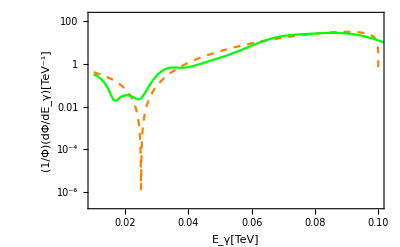

```mathematica
injectionSpectrumPlot1[9999,100, 0.01, 0.1, 0.09,6448777628]
```

Random Seed 6448777628

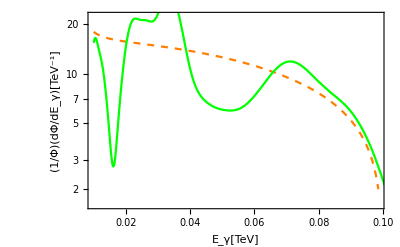

```mathematica
injectionSpectrumPlot1[9999,100, 0.01, 1, 0.09,6448777628]
```

Random Seed 6448777628

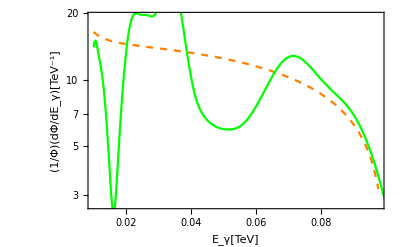

```mathematica
injectionSpectrumPlot1[9999,100, 0.01, 10, 0.09,6448777628]
```

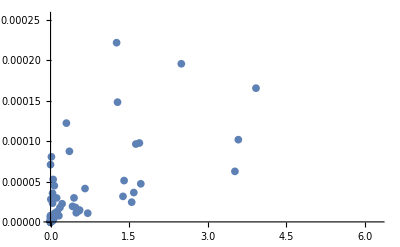

```mathematica
ListPlot[computeAbundanceDecay[9999,100,0]]
```

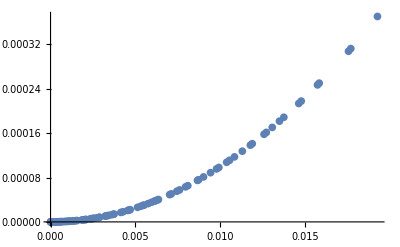

```mathematica
ListPlot[computeAbundance[9999,100,0]]
```

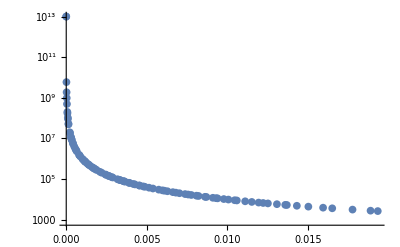

```mathematica
ListLogPlot[computeAnnihilation[9999,100,0]]
```

```mathematica
(*The following plots are intended to show the probability distribution of the random overlap introduced in our decay operator.*)
```

```mathematica
overlap1=Table[computeOverlap[9999,100,0],{1}];
```

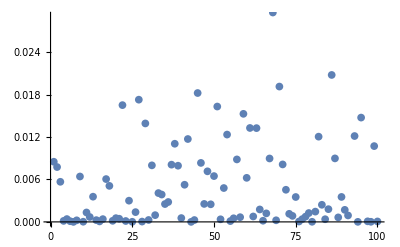

```mathematica
ListPlot[Map[Total[#]/Length[overlap1]&, Transpose[overlap1]]]
```

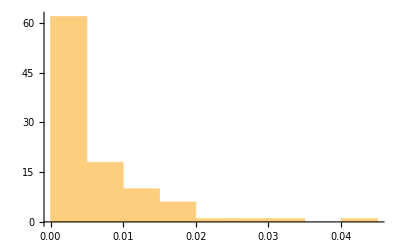

```mathematica
Histogram[First[overlap1]]
```

```mathematica
overlap10=Table[computeOverlap[9999,100,0],{10}];
```

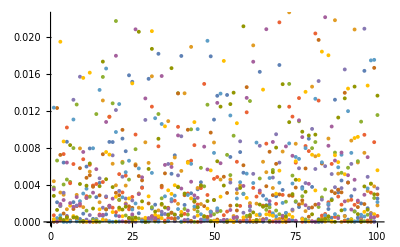

```mathematica
ListPlot[overlap10]
```

```mathematica
overlap100=Table[computeOverlap[9999,100,0],{100}];
```

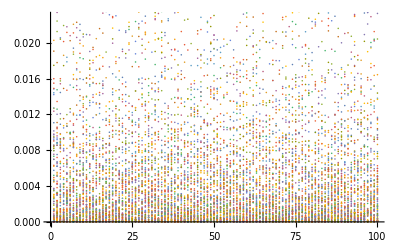

```mathematica
ListPlot[overlap100]
```

{0.627648}

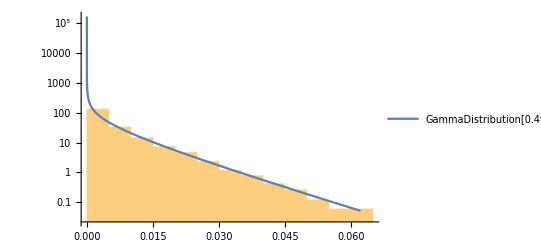

```mathematica
Module[{eigs,eigdata,allparams, dists2, pdfs2, dists={GammaDistribution[alpha, beta]},
pdfs={PDF[GammaDistribution[alpha, beta],xvar]},
inits={{{alpha, 1/2},{beta, 1/100}}}},
eigs = Sort[Flatten[Transpose[overlap100]]];
eigdata = Transpose[{Range[0,Length[eigs]-1], eigs}];
allparams= MapThread[FindDistributionParameters[eigs,#1,#2, ParameterEstimator->{"MaximumLikelihood",Method->"FindMaximum"}] & ,{dists, inits}];
dists2 = MapThread[#1/.#2&,{dists, allparams}];
pdfs2 = MapThread[#1/.#2&,{pdfs, allparams}];
(*Print[eigs];*)
Print[DistributionFitTest[eigs,#]& /@dists2];
Show[{Histogram[eigs,Automatic,{"Log","PDF"}],
LogPlot[pdfs2, {xvar,0,Max[eigs]}, PlotLegends -> dists2]}, PlotRange ->Automatic]]
```

```mathematica
(*The following plots show that the exact GUE PDF is a better match to the data than the Wigner Semicircle PDF.*)
```

```mathematica
(*This is equation 3.13a in the paper.*)
ExactPDFGUE[N_,x_] := E^(-x^2)*Total[Map[HermiteH[#,x]^2/(2^#*#!)&,Range[0,N-1]]]/Sqrt[Pi]
```

```mathematica
ExactPDFGUE1[N_,lambda_, v_] := Module[{x=Sqrt[N]*lambda/(Sqrt[2]*v)}, ExactPDFGUE[N,x]/(Sqrt[2]*v)]
```

```mathematica
DensityOfStates[N_,x_] := 2*ExactPDFGUE[N,N*x/Sqrt[1]]/Sqrt[1]
```

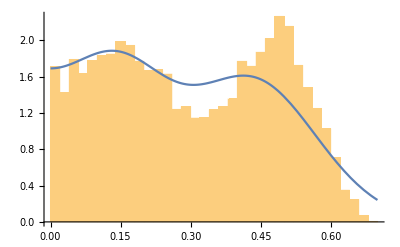

```mathematica
Module[{eigs=Sort[Flatten[Transpose[Table[getEigs[4^2-1,4,0],{2500}]]]]},
Show[Histogram[Map[Sqrt[#]&,eigs],{0,0.7,0.02},"PDF"],Plot[DensityOfStates[4,x],{x,0,0.7}]]]
```

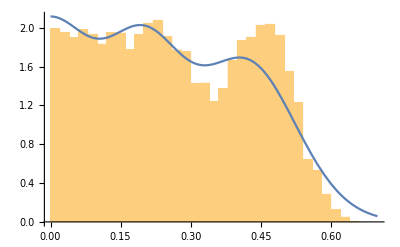

```mathematica
Module[{eigs=Sort[Flatten[Transpose[Table[getEigs[5^2-1,5,0],{2000}]]]]},
Show[Histogram[Map[Sqrt[#]&,eigs],{0,0.7,0.02},"PDF"],Plot[DensityOfStates[5,x],{x,0,0.7}]]]
```

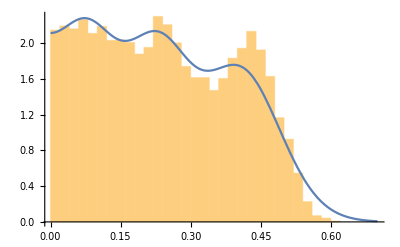

```mathematica
Module[{eigs=Sort[Flatten[Transpose[Table[getEigs[6^2-1,6,0],{1800}]]]]},
Show[Histogram[Map[Sqrt[#]&,eigs],{0,0.7,0.02},"PDF"],Plot[DensityOfStates[6,x],{x,0,0.7}]]]
```

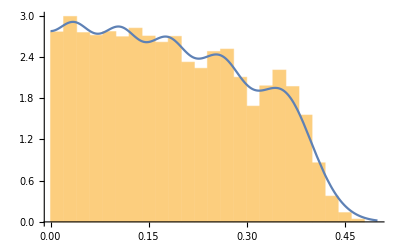

```mathematica
Module[{eigs=Sort[Flatten[Transpose[Table[getEigs[10^2-1,10,0],{1000}]]]]},
Show[Histogram[Map[Sqrt[#]&,eigs],{0,0.5,0.02},"PDF"],Plot[DensityOfStates[10,x],{x,0,0.5}]]]
```

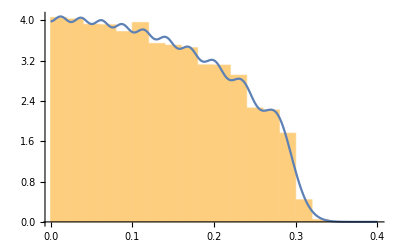

```mathematica
Module[{eigs=Sort[Flatten[Transpose[Table[getEigs[20^2-1,20,0],{500}]]]]},
Show[Histogram[Map[Sqrt[#]&,eigs],{0,0.4,0.02},"PDF"],Plot[DensityOfStates[20,x],{x,0,0.4}]]]
```